(a)
Solving the differential for Lc at steady state gives the following expression:

```mathematica
Solve[0==q+((km*(Lb-Lc))/nc)-kf*Rs*Lc+kr*Rsst,Lc]//FullSimplify
```

{{Lc→(km Lb+nc q+kr nc Rsst)/(km+kf nc Rs)}}

(b)
In the transport limited regime, the following expression results. This is because the EGF concentration on the cell surface is effected by the binding and unbinding of ligand to the receptor and the rate of production, not the bulk concentration of ligand.

```mathematica
Limit[(km Lb+nc q+kr nc Rsst)/(km+kf nc Rs),km->0]//FullSimplify
```

(q+kr Rsst)/(kf Rs)

In the binding limited regime, the EGF concentration at the cell surface is affected by the bulk concentration of ligand.

```mathematica
Limit[(km Lb+nc q+kr nc Rsst)/(km+kf nc Rs),km->Infinity]
```

Lb

(c)

Solve for the the active and inactive surface receptor concentration in terms of km(z) and substitute into the function for L.

```mathematica
Solve[{0==-kf*Lc*Rs+kr*Rsst-ke*Rs+vs,0==kf*Lc*Rs-kr*Rsst-kest*Rsst,0==kest*Rsst-kdeg*Rist,0==ke*Rs-kdeg*Ri,0==q+((km*(-Lc))/nc)-kf*Rs*Lc+kr*Rsst},{Ri,Rs,Rist,Rsst,Lc}]//FullSimplify
```

{{Ri→-1/(2 kdeg kest kf nc)(ke km (kest+kr)+kest kf nc (q-vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Rs→-1/(2 ke kest kf nc)(ke km (kest+kr)+kest kf nc (q-vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Rist→1/(2 kdeg kest kf nc)(ke km (kest+kr)+kest kf nc (q+vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Rsst→1/(2 kest^2 kf nc)(ke km (kest+kr)+kest kf nc (q+vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Lc→-1/(2 kest kf km)(ke km (kest+kr)+kest kf nc (-q+vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs))},{Ri→1/(2 kdeg kest kf nc)(-ke km (kest+kr)+kest kf nc (-q+vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Rs→1/(2 ke kest kf nc)(-ke km (kest+kr)+kest kf nc (-q+vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Rist→1/(2 kdeg kest kf nc)(ke km (kest+kr)+kest kf nc (q+vs)-√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Rsst→1/(2 kest^2 kf nc)(ke km (kest+kr)+kest kf nc (q+vs)-√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs)),Lc→1/(2 kest kf km)(-ke km (kest+kr)+kest kf nc (q-vs)+√((ke km (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km (kest+kr) nc vs))}}

```mathematica
ke=10^-4;
kest=0.005;
kf =5.14*10^-21;
kr=0.025;
kdeg=0.0008;
vs=18;
q=1000;
nc=3*10^8;
```

```mathematica
Kss = (kest*kf)/(ke*(kr+kest))
```

8.56667×10^-18

The total active receptor concentration is analyzed in the limit where Ls*Kss << 1. The total active receptor concentration formula is (7) from the ultrasensitivity lecture notes.

```mathematica
km[z_]:=((100*z^2)/(10^-10))^(1/3)
```

```mathematica
RTfunc[z_] = ((1/kdeg)+(1/kest))*vs*Kss*((nc q+kr nc((ke km [z](kest+kr)+kest kf nc (q+vs)-√((ke km[z] (kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km [z](kest+kr) nc vs))/(2 kest^2 kf nc)))/(km[z]+kf nc ((-ke km [z](kest+kr)+kest kf nc (-q+vs)+√((ke km [z](kest+kr)+kest kf nc (q-vs))^2+4 ke kest kf km[z] (kest+kr) nc vs))/(2 ke kest kf nc))))
```

(2.2359×10^-13 (300000000000+9.72763×10^22 (7.84878×10^-12+0.03 (z^2)^(1/3)-√(1.66536×10^-14 (z^2)^(1/3)+(7.57122×10^-12+0.03 (z^2)^(1/3))^2))))/(10000 (z^2)^(1/3)+1.×10^6 (-7.57122×10^-12-0.03 (z^2)^(1/3)+√(1.66536×10^-14 (z^2)^(1/3)+(7.57122×10^-12+0.03 (z^2)^(1/3))^2)))

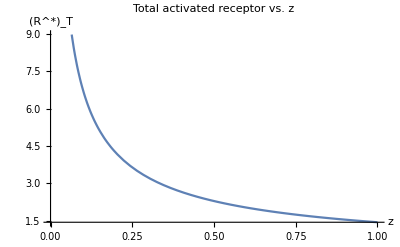

```mathematica
p1=Plot[RTfunc[z],{z,0,0.00000001},AxesLabel->{"z","(R^*)_T"}, PlotLabel->"Total activated receptor vs. z"]
```

Looking at the plot on a nanometer scale, there appears to be a decrease in total activated receptor concentration as z increases. The normalized mitotic rate is equal to the the total activated receptor concentration multiplied by γ, the intrinsic mitogenic signal generation. Therefore the plot clearly shows the mitotic activity decreases as a function of z, since it is proportional to the active receptor concentration times a factor of γ.